```mathematica
ClearAll["Global`*"]
```

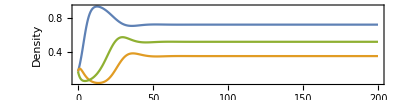

```mathematica
MetapopDyn[α_,λ_,σ_,ρ_,β_,μ_,T_] :=

NDSolve[{
F'[t] ==λ*F[t]-σ*(1-R[t])*F[t] +ρ* R[t] * H[t],
H'[t] ==σ*(1-R[t])*F[t] - ρ* R[t]*H[t] - μ*H[t],
R'[t] ==α*R[t]*(1-R[t]) -(ρ*H[t] + β*F[t])*R[t] ,
F[0]==0.16,H[0]==0.16,R[0]==0.16},{F,H,R},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];

With[{α=0.5,λ=0.2,σ=0.9,ρ=0.1,β=0.2,μ=0.3,T=200},
Traj=Evaluate[{R[t],H[t],F[t]}/.MetapopDyn[α,λ,σ,ρ,β,μ,T] ];
Plot[Traj,{t,0,T},PlotRange->{0,All},AspectRatio->0.25,Frame->True,FrameLabel->{"Time","Density"},PlotLegends->{"R","H","F"}]
]
```

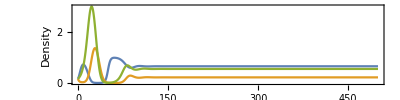
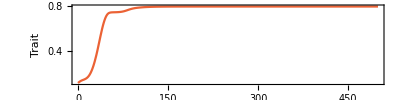
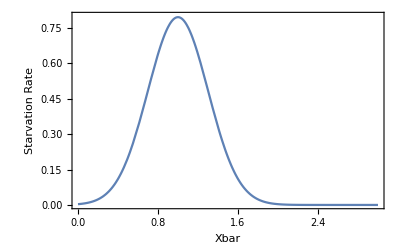

```mathematica
MetapopDyn[α_,λ_,ρ_,β_,μ_,T_,sigmax_,slope_,var_,θ_,varG_] :=(
(*sigma= (sigmax*slope)/(√(var+slope^2))*Exp[(-(xbar[t]-θ)^2)/(2*(var+slope^2))];
Wbar = λ+sigma *(1-R[t])*(F[t]/H[t]-1)+ρ*R[t]*(H[t]/F[t]-R[t])- μ;*)
NDSolve[{
F'[t] ==λ*F[t]-((sigmax*slope)/(√(var+slope^2))*Exp[(-(xbar[t]-θ)^2)/(2*(var+slope^2))])*(1-R[t])*F[t] +ρ* R[t] * H[t],
H'[t] ==((sigmax*slope)/(√(var+slope^2))*Exp[(-(xbar[t]-θ)^2)/(2*(var+slope^2))])*(1-R[t])*F[t] - ρ* R[t]*H[t] - μ*H[t],
R'[t] ==α*R[t]*(1-R[t]) -(ρ*H[t] + β*F[t])*R[t] ,
(*xbar'[t] == varG*D[ λ+( (sigmax*slope)/(√(var+slope^2))*Exp[(-(xbar[t]-θ)^2)/(2*(var+slope^2))] )*(1-R[t])*(F[t]/H[t]-1)+ρ*R[t]*(H[t]/F[t]-R[t]) - μ,xbar[t]],*)
xbar'[t] == varG*D[ λ+( (sigmax*slope)/(√(var+slope^2))*Exp[(-(xbar[t]-θ)^2)/(2*(var+slope^2))] )*(1-R[t])+ρ*R[t]*H[t]/F[t] ,xbar[t]],
F[0]==0.16,H[0]==0.16,R[0]==0.16,xbar[0]==1.6},{F,H,R,xbar},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All]);

With[{α=0.5,λ=0.2,ρ=0.3,β=0.2,μ=0.5,T=500,sigmax=0.8,slope=0.3,var=0.001,θ=1,varG=0.01},
Traj=Evaluate[{R[t],H[t],F[t],xbar[t]}/.MetapopDyn[α,λ,ρ,β,μ,T,sigmax,slope,var,θ,varG] ];
Column[{
Legended[
Show[
Table[
Plot[Traj[[1]][[i]],{t,0,T},PlotRange->{0,All},AspectRatio->0.25,Frame->True,FrameLabel->{"Time","Density"},PlotStyle->ColorData[97,i]],{i,1,3}],ImageSize->400
],SwatchLegend[{ColorData[97,1],ColorData[97,2],ColorData[97,3]},{"R","H","F"}]],

(*Plot[Traj[[1]][[4]],{t,0,T},PlotRange->{0,All},AspectRatio->0.25,Frame->True,FrameLabel->{"Time","Trait"},PlotStyle->ColorData[97,4],ImageSize->400],*)
Plot[(sigmax*slope)/(√(var+slope^2))*Exp[(-(Traj[[1]][[4]]-θ)^2)/(2*(var+slope^2))],{t,0,T},PlotRange->{0,All},AspectRatio->0.25,Frame->True,FrameLabel->{"Time","Trait"},PlotStyle->ColorData[97,4],ImageSize->400],

Plot[(sigmax*slope)/(√(var+slope^2))*Exp[(-(xbar-θ)^2)/(2*(var+slope^2))],{xbar,0,3},Frame->True,FrameLabel->{"Xbar","Starvation Rate"},PlotRange->{0,sigmax}]
}]
]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00408571 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 4.08572 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsvar: 8.16735 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

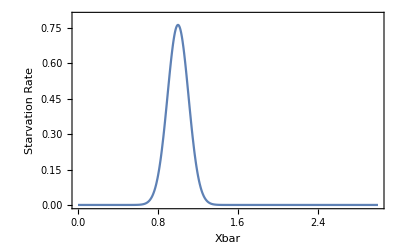
-Graphics-
-Graphics-
-Graphics-

```mathematica
MetapopDyn[α_,λ_,β_,μ_,T_,
sigmax_,slopex_,varx_,θx_,varGx_,
sigmay_,slopey_,vary_,θy_,varGy_] :=(
(*sigma= (sigmax*slope)/(√(var+slope^2))*Exp[(-(xbar[t]-θ)^2)/(2*(var+slope^2))];
Wbar = λ+sigma *(1-R[t])*(F[t]/H[t]-1)+ρ*R[t]*(H[t]/F[t]-R[t])- μ;*)
NDSolve[{
F'[t] ==λ*F[t]-((sigmax*slopex)/(√(varx+slopex^2))*Exp[(-(xbar[t]-θx)^2)/(2*(varx+slopex^2))])*(1-R[t])*F[t] +((sigmay*slopey)/(√(vary+slopey^2))*Exp[(-(ybar[t]-θy)^2)/(2*(vary+slopey^2))])* R[t] * H[t],
H'[t] ==((sigmax*slopex)/(√(varx+slopex^2))*Exp[(-(xbar[t]-θx)^2)/(2*(varx+slopex^2))])*(1-R[t])*F[t] - ((sigmay*slopey)/(√(vary+slopey^2))*Exp[(-(ybar[t]-θy)^2)/(2*(vary+slopey^2))])* R[t]*H[t] - μ*H[t],
R'[t] ==α*R[t]*(1-R[t]) -(ρ*H[t] + β*F[t])*R[t] ,
xbar'[t] ==varGx*D[ λ+( (sigmax*slopex)/(√(varx+slopex^2))*Exp[(-(xbar[t]-θx)^2)/(2*(varx+slopex^2))] )*(1-R[t])*(F[t]/H[t]-1)+((sigmay*slopey)/(√(vary+slopey^2))*Exp[(-(ybar[t]-θy)^2)/(2*(vary+slopey^2))])*R[t]*(H[t]/F[t]-R[t]) - μ,xbar[t]],
ybar'[t] == varGy*D[ λ+( (sigmax*slopex)/(√(varx+slopex^2))*Exp[(-(xbar[t]-θx)^2)/(2*(varx+slopex^2))] )*(1-R[t])*(F[t]/H[t]-1)+((sigmay*slopey)/(√(vary+slopey^2))*Exp[(-(ybar[t]-θy)^2)/(2*(vary+slopey^2))])*R[t]*(H[t]/F[t]-R[t]) - μ,ybar[t]],
F[0]==0.16,H[0]==0.16,R[0]==0.16,xbar[0]==0.8,ybar[0]==0.2},{F,H,R,xbar,ybar},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All]);

With[{α=0.5,λ=0.2,β=0.2,μ=0.3,T=200,
sigmax=0.8,slopex=0.1,varx=0.001,θx=1,varGx=0.1,
sigmay=0.8,slopey=0.1,vary=0.01,θy=1,varGy=0.1},
Traj=Evaluate[{R[t],H[t],F[t],xbar[t],ybar[t]}/.MetapopDyn[α,λ,β,μ,T,
sigmax,slopex,varx,θx,varGx,
sigmay,slopey,vary,θy,varGy] ];
Column[{
Legended[
Show[
Table[
Plot[Traj[[1]][[i]],{t,0,T},PlotRange->{0,All},AspectRatio->0.25,Frame->True,FrameLabel->{"Time","Density"},PlotStyle->ColorData[97,i]],{i,1,3}],ImageSize->400
],SwatchLegend[{ColorData[97,1],ColorData[97,2],ColorData[97,3]},{"R","H","F"}]],

(*Plot[Traj[[1]][[4]],{t,0,T},PlotRange->{0,All},AspectRatio->0.25,Frame->True,FrameLabel->{"Time","Trait"},PlotStyle->ColorData[97,4],ImageSize->400],*)
Plot[{(sigmax*slopex)/(√(varx+slopex^2))*Exp[(-(Traj[[1]][[4]]-θx)^2)/(2*(varx+slopex^2))],(sigmay*slopey)/(√(vary+slopey^2))*Exp[(-(Traj[[1]][[5]]-θy)^2)/(2*(vary+slopey^2))]},{t,0,T},PlotRange->{0,All},AspectRatio->0.25,Frame->True,FrameLabel->{"Time","Trait"},PlotStyle->{ColorData[97,4],ColorData[97,5]},ImageSize->400],

Plot[(sigmax*slopex)/(√(varx+slopex^2))*Exp[(-(xbar-θx)^2)/(2*(varx+slopex^2))],{xbar,0,3},Frame->True,FrameLabel->{"Xbar","Starvation Rate"},PlotRange->{0,sigmax}]
}]
]
```